# Neural Logic Networks for δQL

## Utilities

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

```mathematica
data=ResourceData["663653b1-6151-48ad-b693-3ee813b191c6"];
```

### Feature encoders

```mathematica
Encoders[data_]:=Block[{features=Normal[Keys@First[data]],featureValues},
featureValues={#,Normal[DeleteDuplicates[data[All,#]]]}&/@features;
Association[First[#]->NetEncoder[{"Class",Last[#],"IndicatorVector"}]&/@featureValues]
]
encoders=Encoders[trainData];
inputSize=Total[First[#["Output"]]&/@Normal/@Values[Drop[encoders,-1]]];
classes=Normal[DeleteDuplicates[data[All,"Acceptability"]]];
```

```mathematica
featureLayer=NetGraph[<|"Catenate"->CatenateLayer[]|>,
Map[NetPort[First[#]]->"Catenate"&,Drop[Normal[encoders],-1]],Sequence@@Normal[Drop[Normal[encoders],-1]]
];
```

### Define neural logic net

```mathematica
NeuralLogicNet[]:=Module[{softNet,hardNet,net,trainableNet},
{softNet,hardNet}=HardNeuralChain[{
HardNeuralOR[inputSize,64],
HardNeuralNOT[64,Length[classes]]
}];
net=NetGraph[<|"FeatureLayer"->featureLayer,"SoftNet"->softNet|>,{"FeatureLayer"->"SoftNet"}];
trainableNet=NetGraph[
<|"Net"->net,"Loss"->HardClassificationLoss[]|>,
{NetPort["Acceptability"]->NetPort["Loss","Target"],"Net"->"Loss"},
"Acceptability"->encoders["Acceptability"]
];
{trainableNet,hardNet}
]
```

### Train neural logic net

```mathematica
TrainNeuralLogicNet[net_,trainData_,testData_]:=NetTrain[net,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
TrainingStoppingCriterion->Function[#ValidationLoss<0.02],
Method->{"ADAM"},
TargetDevice->"GPU",
WorkingPrecision->"Real64",
MaxTrainingRounds->Infinity]
```

```mathematica
GetTrainedNeuralLogicNet[result_]:=NetGraph[
<|"TrainedNet"->NetDelete[result["TrainedNet"],"Loss"]|>,
{}
]
```

### Evaluate neural logic net

```mathematica
EvaluateNeuralLogicNet[hardNetFunction_,testData_]:=Module[{predictions,eval},
predictions=HardNetClassify[hardNetFunction,testData,NetDecoder[encoders["Acceptability"]],featureLayer[KeyDrop[#,"Acceptability"]]&,#["Acceptability"]&];eval=HardNetClassifyEvaluation[predictions];
{predictions,eval}
]
```

```mathematica
GetNeuralLogicWeights[trainedNeuralLogicNet_]:=Harden[Flatten[ExtractWeights[trainedNeuralLogicNet]]]
```

## What is δQL?

Just an idea right now. Want to make learnable components a first-class citizen of the QL language.
A QL program is a collection of facts and a collection of logical rules with conditions and actions.
The facts normally represent properties of source code, and the rules deduce whether the code has a security vulnerability.
But the facts and rules can represent anything. For example, here’s a very simple QL program.

```mathematica
Class("Antelope","Mammal")
Class("Lion","Mammal")
Diet("Antelope","Herbivore")
Diet("Lion","Carnivore")
... more facts ...

Danger(X, "High") :- Class(X, "Mammal"), Diet(X, "Carnivore")
Danger(X, "Low") :- Class(X, "Mammal"), Diet(X, "Herbivore")
... more rules ...
```

The rules fire when their conditions are met to create new facts.

```mathematica
Danger("Anteloope", "Low")
Danger("Lion", "High")
```

A δQL program is just a QL program with the addition of learnable rules.

```mathematica
Danger(X, "High") :- Class(X, "Mammal"), Diet(X, "Carnivore")
Danger(X, "Low") :- Class(X, "Mammal"), Diet(X, "Herbivore")

Lifespan(X, Y) :- subsymbolic(Class(X, A), Diet(X, B), Weight(X, C), ...)
```

Learnable rules are “holes” that can appear anywhere in the QL program, which can be filled in from data by learning.

## Why δQL?

- Uniform framework for integrating NN models into QL (e.g. build on success of ATM, but try to avoid complexities and challenges)
- Data-driven rules for static code analysis (replace hand-coded heuristics with data-driven, learnt heuristics). Compete with Snyk, and future-proofing.
- Distilling neural knowledge (e.g. codex) into specialised code-analysis rules (which interact with existing hand-coded knowledge)
- Support future experimentation with QL code synthesis

## Challenges to building δQL

There are lots of challenges! In this talk I’m going to focus on just one of them. Solving this problem is necessary, but not sufficient, for δQL.

Learnable rules can be implemented as neural networks. And, as everyone knows, they learn from data by backpropagation.

Backpropagation works because neural networks, no matter how big they get, are simply differentiable functions.

But we want to learn from input-output data over an entire QL program. For example, we might have examples of real-world code defects, and want to learn good code-analysis heuristics that identify those defects.
But the learnable rules may be embedded deep within a QL program, and therefore surrounded by logical rules. To learn the heuristic we need to back-propagate error signals through logical rules.

And this is the problem: logical rules are discrete, not continuous, objects, and they’re not differentiable.

```mathematica
Danger(X, "High") :- Class(X, "Mammal"), Diet(X, "Carnivore")
```

Now I’m simply going to state, without going into the details, that we can make logical rules differentiable, in the way we want, if we can learn boolean functions by backpropagation. A boolean function is a function from True/False values to True/False values. Here’s an example of one:

```mathematica
bf[x_,y_]:=x&&y
```

```mathematica
bf[True,True]
```

True

```mathematica
bf[True,False]
```

False

But, of course, boolean functions aren’t differentiable either. So we can’t back-propagate error through them.
Hold that thought! Keep it in mind.
Now let’s turn to a learning problem.

## Toy Data

```mathematica
data
```

Dataset[<>]

```mathematica
DeleteDuplicates[Normal[data[All,"Acceptability"]]]
```

This data describes various features of cars -- such as their price, maintenance cost, number of doors and so on. 
We’ll set ourselves the goal of predicting whether a particular car is an acceptable purchase. 
In other words, we want to predict the last column of this table from the first 6 columns.
Let’s split this data into a training and test set.

```mathematica
{trainData,testData}=[data,"TestSetSize"->Scaled[0.1],"Shuffle"->True];
```

## A neural network

Now we define a neural network that can learn this classification problem.

```mathematica
{softNet,hardNet}=NeuralLogicNet[];
```

```mathematica
softNet
```

NetGraph[<>]

This net takes car features as input, converts them to real-valued vectors, processes those inputs, and then outputs 4 probability values (to predict the car’s Acceptability, which is “acceptable”, “unacceptable”, “good” and “very good”) and uses a standard cross-entropy loss.

Notice that we’ve actually defined 2 things here: a soft net, and a hard net. Ignore the hard net for now.

Let’s train it.

```mathematica
result=TrainNeuralLogicNet[softNet,trainData,testData]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:4975  rounds:199  time:20s  examples/s:16673
data | ,,  training examples:1555  validation examples:173  processed examples:318400  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.57×10^-2  error:1.44%
validation | ,,  loss:2.×10^-2  error:0.578%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

I chose the car dataset because it’s quite small, and so I can demo in real-time.
We can see the loss on the training and validation set decreasing.
And we can see the predictive accuracy of the net increasing.
It takes about 30 seconds to get high accuracy on the validation set.
Once trained, we can extract the trained classifier.

```mathematica
trainedNeuralLogicNet=GetTrainedNeuralLogicNet[result];
```

Now, when we defined the neural-logic net we got 2 things: what I called a soft net and a hard net.
These are 2 different representations of the same network architecture.
The soft net uses real weights, and is a differentiable nonlinear function.
The hard net uses boolean weights, and is a non-differentiable, discrete boolean function.

Now comes the trick!

```mathematica
diagram=Import["/home/wright/Downloads/neural-logic-net.png"]
```

-Graphics-

We use the soft net to learn real-valued weights.
Then we convert the real-valued weights to boolean-valued weights, just True and False.
And then we use the boolean weights with the hard net.
Unlike existing binarization techniques this conversion is perfect ... we don’t introduce any approximation error.

Let’s do this now.

```mathematica
hnf=HardNetFunction[hardNet,trainedNeuralLogicNet];
hnbe=HardNetBooleanExpression[hnf,inputSize]
```

{{!(b2||b3||b7||b8||b13||b18||b20),b2||b3||b7||b8||b11||b12||b13||b16||b20||b21,b7||b8||b11||b13||b21,b2||b3||b7||b8||b11||b13||b16||b19||b21,!(b17||b18||b19),b2||b3||b13||b16||b20||b21,!(b3||b8||b16||b17||b20),b2||b8||b11||b13||b16||b21,!(b1||b4||b7),b2||b3||b6||b13||b20||b21,b7||b19||b20||b21,b3||b7||b11||b13||b21,b2||b13||b16||b21,!(b9||b10||b16||b18),!(b17||b19||b20),b13||b14||b16||b21,b3||b7||b8||b9||b13||b15||b18||b21,!(b2||b3||b8||b11||b20),b2||b5||b6||b13||b16||b21,!(b9||b10||b15||b16||b18),b2||b3||b11||b13||b14||b16||b18||b21,b2||b11||b13||b18||b21,b2||b8||b13||b16||b21,b1||b7||b8||b13||b21,!(b2||b3||b8||b9||b10||b16||b17||b20),!(b1||b4),b2||b3||b4||b8||b16||b21,!(b1||b5||b11||b14||b16),b1||b4||b7||b8||b13||b16||b21,!(b1||b5),b2||b3||b8||b11||b13||b16||b20||b21,b1||b4||b7||b8||b13||b20||b21,b2||b5||b8||b11||b13||b21,!(b4||b6||b7||b18||b19),b2||b3||b13||b19||b21,b3||b8||b9||b10||b13||b16||b17||b21,b2||b4||b6||b8||b13||b21,b2||b3||b7||b8||b13||b20||b21,!(b11||b17||b18||b19),b7||b9||b10||b13||b18||b20,b7||b8||b11||b13||b14||b16||b19||b21,!(b5||b18||b19),b4||b8||b13||b21,b3||b7||b8||b13||b16||b21,!(b1||b5||b6||b19),!(b9||b12||b14||b17||b18),!(b8||b11||b15||b16),!(b3||b6||b7||b8||b10||b11||b12||b17),b3||b7||b13||b16||b21,!(b1||b2||b3||b5||b13||b21),b2||b5||b13||b21,b8||b13||b16||b21,b2||b8||b11||b13||b21,!(b9||b10||b15||b16||b18),b2||b3||b4||b8||b13||b18||b19||b21,b2||b3||b7||b8||b13||b21,!(b9||b10||b11||b13||b15||b18||b19),b1||b2||b8||b13||b20||b21,b3||b7||b13||b21,!(b1||b4||b7||b19),b2||b9||b10||b13||b15||b18||b20||b21,!(b6||b10||b12||b14||b18||b19),b3||b7||b8||b11||b13||b21,b12||b13||b15||b17||b21},{!(b2||b3||b7||b8||b13||b18||b20),b2||b3||b7||b8||b11||b12||b13||b16||b20||b21,!(b7||b8||b11||b13||b21),!(b2||b3||b7||b8||b11||b13||b16||b19||b21),b17||b18||b19,b2||b3||b13||b16||b20||b21,b3||b8||b16||b17||b20,!(b2||b8||b11||b13||b16||b21),b1||b4||b7,!(b2||b3||b6||b13||b20||b21),!(b7||b19||b20||b21),!(b3||b7||b11||b13||b21),!(b2||b13||b16||b21),b9||b10||b16||b18,!(b17||b19||b20),!(b13||b14||b16||b21),b3||b7||b8||b9||b13||b15||b18||b21,!(b2||b3||b8||b11||b20),b2||b5||b6||b13||b16||b21,b9||b10||b15||b16||b18,b2||b3||b11||b13||b14||b16||b18||b21,!(b2||b11||b13||b18||b21),!(b2||b8||b13||b16||b21),b1||b7||b8||b13||b21,b2||b3||b8||b9||b10||b16||b17||b20,b1||b4,!(b2||b3||b4||b8||b16||b21),b1||b5||b11||b14||b16,b1||b4||b7||b8||b13||b16||b21,b1||b5,b2||b3||b8||b11||b13||b16||b20||b21,b1||b4||b7||b8||b13||b20||b21,!(b2||b5||b8||b11||b13||b21),!(b4||b6||b7||b18||b19),!(b2||b3||b13||b19||b21),!(b3||b8||b9||b10||b13||b16||b17||b21),b2||b4||b6||b8||b13||b21,!(b2||b3||b7||b8||b13||b20||b21),b11||b17||b18||b19,!(b7||b9||b10||b13||b18||b20),!(b7||b8||b11||b13||b14||b16||b19||b21),b5||b18||b19,!(b4||b8||b13||b21),!(b3||b7||b8||b13||b16||b21),b1||b5||b6||b19,b9||b12||b14||b17||b18,!(b8||b11||b15||b16),!(b3||b6||b7||b8||b10||b11||b12||b17),!(b3||b7||b13||b16||b21),b1||b2||b3||b5||b13||b21,b2||b5||b13||b21,!(b8||b13||b16||b21),!(b2||b8||b11||b13||b21),b9||b10||b15||b16||b18,b2||b3||b4||b8||b13||b18||b19||b21,!(b2||b3||b7||b8||b13||b21),b9||b10||b11||b13||b15||b18||b19,b1||b2||b8||b13||b20||b21,!(b3||b7||b13||b21),b1||b4||b7||b19,!(b2||b9||b10||b13||b15||b18||b20||b21),b6||b10||b12||b14||b18||b19,!(b3||b7||b8||b11||b13||b21),!(b12||b13||b15||b17||b21)},{b2||b3||b7||b8||b13||b18||b20,b2||b3||b7||b8||b11||b12||b13||b16||b20||b21,!(b7||b8||b11||b13||b21),b2||b3||b7||b8||b11||b13||b16||b19||b21,b17||b18||b19,b2||b3||b13||b16||b20||b21,b3||b8||b16||b17||b20,!(b2||b8||b11||b13||b16||b21),b1||b4||b7,!(b2||b3||b6||b13||b20||b21),b7||b19||b20||b21,!(b3||b7||b11||b13||b21),!(b2||b13||b16||b21),b9||b10||b16||b18,b17||b19||b20,!(b13||b14||b16||b21),!(b3||b7||b8||b9||b13||b15||b18||b21),b2||b3||b8||b11||b20,!(b2||b5||b6||b13||b16||b21),!(b9||b10||b15||b16||b18),b2||b3||b11||b13||b14||b16||b18||b21,!(b2||b11||b13||b18||b21),b2||b8||b13||b16||b21,!(b1||b7||b8||b13||b21),b2||b3||b8||b9||b10||b16||b17||b20,b1||b4,b2||b3||b4||b8||b16||b21,b1||b5||b11||b14||b16,!(b1||b4||b7||b8||b13||b16||b21),!(b1||b5),b2||b3||b8||b11||b13||b16||b20||b21,!(b1||b4||b7||b8||b13||b20||b21),!(b2||b5||b8||b11||b13||b21),b4||b6||b7||b18||b19,!(b2||b3||b13||b19||b21),b3||b8||b9||b10||b13||b16||b17||b21,!(b2||b4||b6||b8||b13||b21),b2||b3||b7||b8||b13||b20||b21,b11||b17||b18||b19,b7||b9||b10||b13||b18||b20,!(b7||b8||b11||b13||b14||b16||b19||b21),b5||b18||b19,!(b4||b8||b13||b21),b3||b7||b8||b13||b16||b21,b1||b5||b6||b19,b9||b12||b14||b17||b18,b8||b11||b15||b16,b3||b6||b7||b8||b10||b11||b12||b17,!(b3||b7||b13||b16||b21),!(b1||b2||b3||b5||b13||b21),!(b2||b5||b13||b21),!(b8||b13||b16||b21),!(b2||b8||b11||b13||b21),b9||b10||b15||b16||b18,!(b2||b3||b4||b8||b13||b18||b19||b21),b2||b3||b7||b8||b13||b21,b9||b10||b11||b13||b15||b18||b19,!(b1||b2||b8||b13||b20||b21),!(b3||b7||b13||b21),b1||b4||b7||b19,!(b2||b9||b10||b13||b15||b18||b20||b21),b6||b10||b12||b14||b18||b19,!(b3||b7||b8||b11||b13||b21),!(b12||b13||b15||b17||b21)},{!(b2||b3||b7||b8||b13||b18||b20),!(b2||b3||b7||b8||b11||b12||b13||b16||b20||b21),!(b7||b8||b11||b13||b21),b2||b3||b7||b8||b11||b13||b16||b19||b21,!(b17||b18||b19),!(b2||b3||b13||b16||b20||b21),!(b3||b8||b16||b17||b20),!(b2||b8||b11||b13||b16||b21),b1||b4||b7,!(b2||b3||b6||b13||b20||b21),!(b7||b19||b20||b21),!(b3||b7||b11||b13||b21),!(b2||b13||b16||b21),b9||b10||b16||b18,!(b17||b19||b20),!(b13||b14||b16||b21),b3||b7||b8||b9||b13||b15||b18||b21,!(b2||b3||b8||b11||b20),b2||b5||b6||b13||b16||b21,b9||b10||b15||b16||b18,!(b2||b3||b11||b13||b14||b16||b18||b21),!(b2||b11||b13||b18||b21),!(b2||b8||b13||b16||b21),!(b1||b7||b8||b13||b21),!(b2||b3||b8||b9||b10||b16||b17||b20),b1||b4,!(b2||b3||b4||b8||b16||b21),b1||b5||b11||b14||b16,b1||b4||b7||b8||b13||b16||b21,b1||b5,!(b2||b3||b8||b11||b13||b16||b20||b21),b1||b4||b7||b8||b13||b20||b21,!(b2||b5||b8||b11||b13||b21),b4||b6||b7||b18||b19,b2||b3||b13||b19||b21,!(b3||b8||b9||b10||b13||b16||b17||b21),!(b2||b4||b6||b8||b13||b21),!(b2||b3||b7||b8||b13||b20||b21),b11||b17||b18||b19,b7||b9||b10||b13||b18||b20,b7||b8||b11||b13||b14||b16||b19||b21,b5||b18||b19,!(b4||b8||b13||b21),!(b3||b7||b8||b13||b16||b21),b1||b5||b6||b19,b9||b12||b14||b17||b18,!(b8||b11||b15||b16),!(b3||b6||b7||b8||b10||b11||b12||b17),!(b3||b7||b13||b16||b21),b1||b2||b3||b5||b13||b21,!(b2||b5||b13||b21),!(b8||b13||b16||b21),!(b2||b8||b11||b13||b21),b9||b10||b15||b16||b18,b2||b3||b4||b8||b13||b18||b19||b21,!(b2||b3||b7||b8||b13||b21),!(b9||b10||b11||b13||b15||b18||b19),b1||b2||b8||b13||b20||b21,b3||b7||b13||b21,b1||b4||b7||b19,b2||b9||b10||b13||b15||b18||b20||b21,b6||b10||b12||b14||b18||b19,!(b3||b7||b8||b11||b13||b21),!(b12||b13||b15||b17||b21)}}

This expression is a Boolean function. Each b, from 1 to 21, is a single input bit, which together represent a car’s features.

Notice that the boolean function is a combination of NOTs and ORs, which corresponds to the architecture of the neural-logic net, which I’ll explain in a moment.

```mathematica
Drop[testData[[1]],-1]
```

```mathematica
Normal[featureLayer[%]]
```

{0,0,1,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,1,0,0}

```mathematica
Harden[%]
```

{False,False,True,False,False,True,False,False,False,False,True,False,True,False,False,False,False,True,True,False,False}

The output is a vector of boolean values which can be interpreted as a probability distribution.

```mathematica
hnf[%]
```

{{False,True,True,True,False,True,False,True,True,True,True,True,True,False,False,True,True,False,True,False,True,True,True,True,False,True,True,False,True,True,True,True,True,False,True,True,True,True,False,True,True,False,True,True,False,False,False,False,True,False,True,True,True,False,True,True,False,True,True,False,True,False,True,True},{False,True,False,False,True,True,True,False,False,False,False,False,False,True,False,False,True,False,True,True,True,False,False,True,True,False,False,True,True,False,True,True,False,False,False,False,True,False,True,False,False,True,False,False,True,True,False,False,False,True,True,False,False,True,True,False,True,True,False,True,False,True,False,False},{True,True,False,True,True,True,True,False,False,False,True,False,False,True,True,False,False,True,False,False,True,False,True,False,True,False,True,True,False,True,True,False,False,True,False,True,False,True,True,True,False,True,False,True,True,True,True,True,False,False,False,False,False,True,False,True,True,False,False,True,False,True,False,False},{False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,True,False,True,True,False,False,False,False,False,False,False,True,True,False,False,True,False,True,True,False,False,False,True,True,True,True,False,False,True,True,False,False,False,True,False,False,False,True,True,False,False,True,True,True,True,True,False,False}}

Now we have a learnt boolean function that can predict the acceptability of a car.
Let’s evaluate it on the test data.

```mathematica
{predictions,summary}=EvaluateNeuralLogicNet[hnf,testData];
```

We can eyeball the predictions of the net compared to the ground truth.

```mathematica
RandomSample[predictions,3]
```

{<|Prediction→acceptable,Target→acceptable|>,<|Prediction→unacceptable,Target→unacceptable|>,<|Prediction→unacceptable,Target→unacceptable|>}

And we can measure the overall accuracy of the net.

```mathematica
summary["Accuracy"]
```

0.99422

This is pretty amazing. We’ve trained a neural network, using gradient descent on a GPU, but we get a discrete boolean function. We’re extending the power of gradient descent into the world of discrete functions. And we’ve got a POC solution to one of the challenges to creating δQL.

But we get another bonus from this approach. Let’s take a look at the learned weights.

```mathematica
neuralLogicWeights=GetNeuralLogicWeights[result["TrainedNet"]]
```

So the weights can be compactly represented as bit vectors. Each weight costs 1 bit. So the total size of this classifier is very small.

```mathematica
neuralLogicNetSize=Quantity[Length[neuralLogicWeights]/8/1024//N,"Kilobytes"]
```

0.195313 kB

In fact, in this case the neural-logic classifier is 80 times smaller than standard net on the same problem (which is about 15k). That’s a lot smaller.
That means we can ship lots more NNs with QL without hitting OOM errors in standard environments.

Also, evaluating a boolean function can be a lot cheaper than evaluating a nonlinear real-valued function.
Different kinds of machine learning problems will generate different kinds of savings.
But neural-logic nets are always going to be smaller.

How does this work? Basically by defining an entirely new kind of neural network architecture.

```mathematica
Information[softNet,"FullSummaryGraphic"]
```

-Graphics-

I chose this architecture because it’s the smallest neural-logic network that can learn the classification problem.
The first layer consists of 64 neurons that act like the logical OR operator but are continuous functions and therefore differentiable.
The second layer consists of 4 neurons that act like the logical NOT operator but are also differentiable.
The learnable real-valued weights in this net are real-valued “soft bits” that range between 0 and 1.
They control whether specific OR or NOT operations are active.
Although the semantics correspond to non-differentiable logical operations the entire net is end-to-end differentiable.
But the activation functions are quite unlike normal neural networks.
Plus, there are additional special neural components, which ensure we can train it like a normal neural network.

So training takes longer.
Neural-logic nets have the same worst-case time-complexity as standard nets but there is a constant cost to pay.
But the additional training costs yield the benefit of very compact classifiers that are cheap to query and have the same predictive performance, as we’re about to see.

And we build boolean function analogues of all the existing kinds of neural network architectures.
And this kind of network is just the kind of thing we need to integrate NN learning with QL at a fundamental level.
That’s it for now!
Want to find out more? Visit the repo: https://github.com/github/neural-logic

## Notes

```mathematica
{trainedSoftNet,trainedHardNet}=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[#],"Loss/Error"]|>,
{},"Output"->NetDecoder[encoders["Acceptability"]]
]&/@{result["TrainedNet"],HardenNet[result["TrainedNet"]]};
```

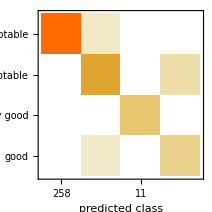
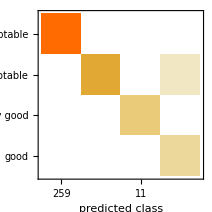
{Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (98.80.6) %
Accuracy baseline | (74.92.3) %
Geometric mean of probabilities | 0.973 ± 0.013
Mean cross entropy | 0.0273 ± 0.014
Single evaluation time | 6.86 ms/example
Batch evaluation speed | 1.34 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (99.40.4) %
Accuracy baseline | (74.92.3) %
Geometric mean of probabilities | 0.974 ± 0.014
Mean cross entropy | 0.026 ± 0.015
Single evaluation time | 7.02 ms/example
Batch evaluation speed | 1.08 examples/ms
-Graphics- | }

```mathematica
ClassifierMeasurements[#,testData->"Acceptability"]&/@{trainedSoftNet,trainedHardNet}
```

```mathematica
hncwt2=Association[{"Prediction"->trainedHardNet[KeyDrop[{"Acceptability"}]@#],"Target"->#["Acceptability"]}]&/@Normal[testData];
eval2=HardNetClassifyEvaluation[hncwt2];
eval2["Accuracy"]
```

0.99422